## Reconstrucción del mapa de parámetros

En esta sección intenemos reproducir el mapa de bifurcación
-Graphics-
Los parámetros son I_2 la intensidad de corriente antes de la señal y ΔI, la magnitud del salto

```mathematica
Cm=1; 
ENa=115;gNa=120;
EK=-12; gK=36;
EL=10.6;gL=0.3;
```

```mathematica
αn[u_] =(0.1-0.01 u)/(Exp[1-0.1 u]-1); βn[u_] = 0.125 Exp[-u/80];
τn[u_] = 1/(αn[u]+βn[u]);no[u_] = αn[u]/(αn[u]+βn[u]);
αm[u_] =(2.5-0.1 u)/(Exp[2.5-0.1 u]-1); βm[u_] = 4  Exp[-u/18];
τm[u_] = 1/(αm[u]+βm[u]);mo[u_] = αm[u]/(αm[u]+βm[u]);
αh[u_] =0.07 Exp[-u/20]; βh[u_] =1/  (Exp[3-0.1 u]+1);
τh[u_] = 1/(αh[u]+βh[u]);ho[u_] = αh[u]/(αh[u]+βh[u]);
```

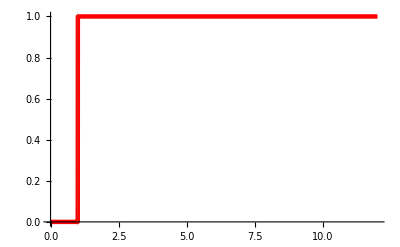

```mathematica
Plot[UnitStep[t-1],{t,0,12},PlotStyle->{Thickness[.008],Red},GridLines->{{1},None}]
```

```mathematica
Clear[A,a,I2]
```

```mathematica
J1[dI2_,a_,I2_] :=I2+ dI2 UnitStep[t-a]
```

```mathematica
tmax=100
```

100

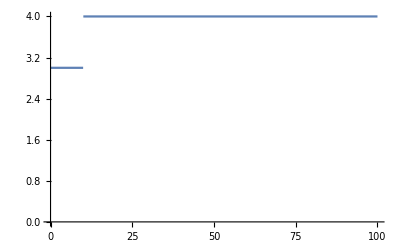

```mathematica
Plot[J1[1,10,3],{t,0,tmax},AxesOrigin->{0,0}]
```

```mathematica
init={u[-10]==0,m[-10]==0,n[-10]==0,h[-10]==0}
```

{u[-10]==0,m[-10]==0,n[-10]==0,h[-10]==0}

```mathematica
HH3[dI2_,a_,I2_]:={
Cm u'[t]== -gNa m[t]^3 h[t] (u[t]-ENa) -gK  n[t]^4  (u[t]-EK) - gL (u[t]-EL) +J1[dI2,a,I2],
m'[t]==αm[u[t]] (1-m[t]) - βm[u[t]] m[t],
n'[t]==αn[u[t]] (1-n[t]) - βn[u[t]] n[t],
h'[t]==αh[u[t]] (1-h[t]) - βh[u[t]]h[t]}
```

```mathematica
HH3[4,0,3]
```

{u'[t]==3-120 h[t] m[t]^3 (-115+u[t])-0.3 (-10.6+u[t])-36 n[t]^4 (12+u[t])+4 UnitStep[t],m'[t]==-4 ⅇ^(-u[t]/18) m[t]+((1-m[t]) (2.5-0.1 u[t]))/(-1+ⅇ^(2.5-0.1 u[t])),n'[t]==-0.125 ⅇ^(-u[t]/80) n[t]+((1-n[t]) (0.1-0.01 u[t]))/(-1+ⅇ^(1-0.1 u[t])),h'[t]==0.07 ⅇ^(-u[t]/20) (1-h[t])-h[t]/(1+ⅇ^(3-0.1 u[t]))}

```mathematica
sol1=NDSolve[Join[init,HH3[.5,0,0.5]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
```

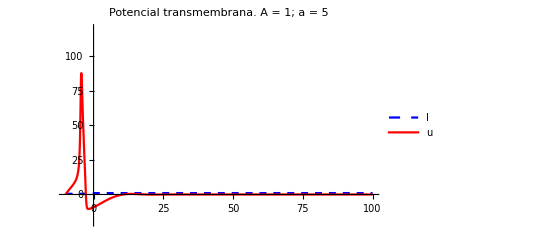

```mathematica
Plot[{J1[.5,0,0.5],u[t]/.sol1},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = 1; a = 5",PlotLegends->{"I","u"},PlotRange-> All]
```

```mathematica
Manipulate[
sol1=NDSolve[Join[init,HH3[dI2,a,I2]],{u[t],m[t],n[t] ,h[t]},{t,-10,tmax}]//Flatten;
Plot[{J1[dI2,a,I2],u[t]/.sol1},{t,-10,tmax},PlotStyle->{{Dashed,Blue},Red},PlotRange -> {-20,120},PlotLabel-> "Potencial transmembrana. A = "<>ToString[A],PlotLegends->{"I","u"},PlotRange-> All],{dI2,0,6,.1},{a,0,15},{I2,0,8,.1}
]
```

NDSolve::deqn: Equation or list of equations expected instead of 
    Join[init, HH3[5., 0, 5.1]] in the first argument 
    Join[init, HH3[5., 0, 5.1]].

Plot::plln: Limiting value tmax in {t, -10, tmax}
     is not a machine-sized real number.